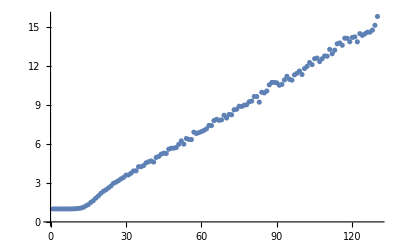

```mathematica
pc[n_,r_]:=Module[{list=Table[{i},{i,n}],choice,union,i},
For[i=1,i<=r,i++,
choice={{},{}};
While[choice[[1]]==choice[[2]],
choice=RandomInteger[{1,n-i+1},2];
];
union=Union[list[[choice[[1]]]],list[[choice[[2]]]]];
list=Append[Delete[list,{{choice[[1]]},{choice[[2]]}}],union];
];
Return[list];
]
dpc[n_,r_]:=Map[Length,pc[n,r]];
mdpc[n_,r_,m_]:=Map[N@*Mean,Table[dpc[n,r],{i,m}]ᵀ];
ListPlot[mdpc[1000,870,1000]]
```